Initialize functions

```mathematica
(*Ensure that variables are defined globally*)
SetOptions[EvaluationNotebook[],CellContext->"Global`"]
NotebookOpen[NotebookDirectory[]<>"GB-strain-scattering_init.nb"];
NotebookEvaluate[NotebookDirectory[]<>"GB-strain-scattering_init.nb"];
```

Define material values and phonon dispersion parameters

```mathematica
(*#############################*)
(*### Material values for Si ###*)
(*#############################*)

(*#### crystal properties ####*)
vs=6084. (*[m/s] average speed of sound*);
V=2*10^-29 (*[m^3] volume of atom*);
n=2(*# atoms per primitive unit cell (N in paper)*);
γ=1(*Gruneissen parameter*);
ν=0.27(*Poisson's ratio*);
kmax=k0[V*n]//N(*[m^-1] edge of FBZ*);
ωD=vs kmax(*[s^-1] Debye frequency*);
disp="Debye";
ωk[k_]:=vs k (*Debye dispersion relation*);
vg[k_]:=vs (*phonon group velocity*);

(*#### phonon-phonon ####*)
C1=2.69*10^-19 (*[s/K]*);
C2=167(*[K]*);

(*#### point defect ####*)
C3=1.81*10^-45 (*[s^3]*);

(*#### microstructure ####*)
b=(V n)^(1/3)(*[m] Burger's vector*);
dGS=350*10^-9 (*[m] average grain size*);
n1D=3/dGS//N(*[m^-1] number density of GBs *);
d=3*10^-9 (*[m] GB dislocation spacing (D in paper)*);
```

Diffraction peaks in Γ_gbs(k)

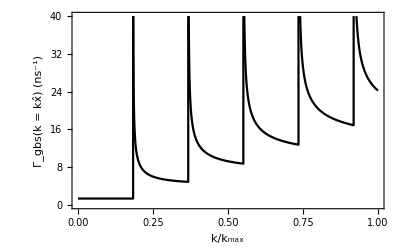

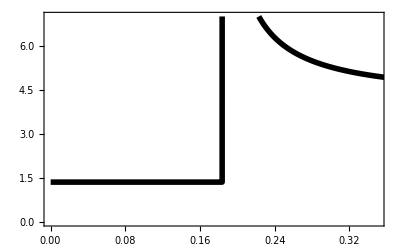

```mathematica
ΓMakeList[θ_,ϕ_]:=Table[{ω/ωD,ΓGBS[ω/vs,θ,ϕ]*10^-9},{ω,0,ωD,10^10}];
(*θ=π/2 ϕ=0 is phonon incident normal to the GB.*)
ΓlistGBS=ΓMakeList[π/2,0];

ListPlot[{ΓlistGBS},
PlotStyle->{Black},
PlotRange->{{0,1},{0,40}},
Joined->True,
FrameLabel->{"k/k_max","Γ_gbs(k = kx̂) (ns^-1)"}]

ListPlot[{ΓlistGBS},
Joined->True,
FrameStyle->Directive[FontFamily->"Times New Roman",FontSize->20,Black],
PlotStyle->Directive[Black,Thickness[0.01]],
PlotRange->{{0,0.35},{0,7}}]
```

Calculating (τ_gbs(ω))^-1

```mathematica
(*A convergence test was perfomed on δk by caluclating κL at different δk. δk=2*10^8 was found to be fully converged. This calculation takes ~20 min on most personal computers*)
Clear[d]
τGBSList={disp};
δk=2.*10^8;
For[d=1.0*10^-9,d≤8.0*10^-9,d=d*2.0,
Print[d];
τGBSListd=Table[{ω/vs,τGBSθϕIntegrate[ω/vs,90]},{ω,vs δk,ωD,vs δk}];
AppendTo[τGBSList,{d,θcalc[b,d],τGBSListd}]
]
```

1.×10^-9

2.×10^-9

4.×10^-9

8.×10^-9

```mathematica
(*############################*)
(*#### Exports τGBS results ###*)
(*############################*)
Export[NotebookDirectory[]<>"../Results/tauSTGB_results.m",τGBSList]
```

/Users/rileyhanus/Desktop/Papers/Phonon_diffraction/Scripts/FOR_DISTRIBUTION/Phonon-scattering-and-transport-in-polycyrstals/core/../Results/tauSTGB_results.m

```mathematica
(*##############################################*)
(*#### Imports the last exported τGBS result ####*)
(*##############################################*)
τGBSList=Import[NotebookDirectory[]<>"../Results/tauSTGB_results.m"];
```

{Debye,{1.×10^-9,19.4072,{{2.×10^8,6.14821×10^-11},{4.×10^8,6.14821×10^-11},{6.×10^8,6.14821×10^-11},{8.×10^8,6.14821×10^-11},{1.×10^9,6.14821×10^-11},{1.2×10^9,6.14821×10^-11},{1.4×10^9,6.14821×10^-11},{1.6×10^9,6.14821×10^-11},{1.8×10^9,6.14821×10^-11},{2.×10^9,6.14821×10^-11},{2.2×10^9,6.14821×10^-11},{2.4×10^9,6.14821×10^-11},{2.6×10^9,6.14821×10^-11},{2.8×10^9,6.14821×10^-11},{3.×10^9,6.14821×10^-11},{3.2×10^9,6.14756×10^-11},{3.4×10^9,6.12131×10^-11},{3.6×10^9,6.04159×10^-11},{3.8×10^9,5.91607×10^-11},{4.×10^9,5.75043×10^-11},{4.2×10^9,5.55642×10^-11},{4.4×10^9,5.3422×10^-11},{4.6×10^9,5.1207×10^-11},{4.8×10^9,4.88423×10^-11},{5.×10^9,4.65701×10^-11},{5.2×10^9,4.4243×10^-11},{5.4×10^9,4.21116×10^-11},{5.6×10^9,3.98732×10^-11},{5.8×10^9,3.78726×10^-11},{6.×10^9,3.59603×10^-11},{6.2×10^9,3.40332×10^-11},{6.4×10^9,3.25353×10^-11},{6.6×10^9,3.1609×10^-11},{6.8×10^9,3.07381×10^-11},{7.×10^9,2.99507×10^-11},{7.2×10^9,2.92405×10^-11},{7.4×10^9,2.84182×10^-11},{7.6×10^9,2.76237×10^-11},{7.8×10^9,2.68466×10^-11},{8.×10^9,2.6078×10^-11},{8.2×10^9,2.52033×10^-11},{8.4×10^9,2.44094×10^-11},{8.6×10^9,2.35855×10^-11},{8.8×10^9,2.28058×10^-11},{9.×10^9,2.20237×10^-11},{9.2×10^9,2.13643×10^-11},{9.4×10^9,2.05386×10^-11},{9.6×10^9,1.99589×10^-11},{9.8×10^9,1.95639×10^-11},{1.×10^10,1.9191×10^-11},{1.02×10^10,1.88106×10^-11},{1.04×10^10,1.8487×10^-11},{1.06×10^10,1.81036×10^-11},{1.08×10^10,1.77225×10^-11},{1.1×10^10,1.73942×10^-11},{1.12×10^10,1.695×10^-11}}},{2.×10^-9,9.77367,{{2.×10^8,2.45928×10^-10},{4.×10^8,2.45928×10^-10},{6.×10^8,2.45928×10^-10},{8.×10^8,2.45928×10^-10},{1.×10^9,2.45928×10^-10},{1.2×10^9,2.45928×10^-10},{1.4×10^9,2.45928×10^-10},{1.6×10^9,2.45902×10^-10},{1.8×10^9,2.41664×10^-10},{2.×10^9,2.30017×10^-10},{2.2×10^9,2.13688×10^-10},{2.4×10^9,1.95369×10^-10},{2.6×10^9,1.76972×10^-10},{2.8×10^9,1.59493×10^-10},{3.×10^9,1.43841×10^-10},{3.2×10^9,1.30141×10^-10},{3.4×10^9,1.22952×10^-10},{3.6×10^9,1.16962×10^-10},{3.8×10^9,1.10495×10^-10},{4.×10^9,1.04312×10^-10},{4.2×10^9,9.76375×10^-11},{4.4×10^9,9.12231×10^-11},{4.6×10^9,8.54573×10^-11},{4.8×10^9,7.98358×10^-11},{5.×10^9,7.67642×10^-11},{5.2×10^9,7.39481×10^-11},{5.4×10^9,7.08899×10^-11},{5.6×10^9,6.78×10^-11},{5.8×10^9,6.4974×10^-11},{6.×10^9,6.20301×10^-11},{6.2×10^9,5.87833×10^-11},{6.4×10^9,5.64809×10^-11},{6.6×10^9,5.48868×10^-11},{6.8×10^9,5.32247×10^-11},{7.×10^9,5.15695×10^-11},{7.2×10^9,4.99971×10^-11},{7.4×10^9,4.81373×10^-11},{7.6×10^9,4.63122×10^-11},{7.8×10^9,4.46009×10^-11},{8.×10^9,4.34284×10^-11},{8.2×10^9,4.24252×10^-11},{8.4×10^9,4.12828×10^-11},{8.6×10^9,4.03482×10^-11},{8.8×10^9,3.92156×10^-11},{9.×10^9,3.81421×10^-11},{9.2×10^9,3.7164×10^-11},{9.4×10^9,3.58856×10^-11},{9.6×10^9,3.51807×10^-11},{9.8×10^9,3.44019×10^-11},{1.×10^10,3.38001×10^-11},{1.02×10^10,3.29803×10^-11},{1.04×10^10,3.2334×10^-11},{1.06×10^10,3.15222×10^-11},{1.08×10^10,3.07476×10^-11},{1.1×10^10,2.99906×10^-11},{1.12×10^10,2.94521×10^-11}}},{4.×10^-9,4.89574,{{2.×10^8,9.83714×10^-10},{4.×10^8,9.83714×10^-10},{6.×10^8,9.83714×10^-10},{8.×10^8,9.83609×10^-10},{1.×10^9,9.2007×10^-10},{1.2×10^9,7.81477×10^-10},{1.4×10^9,6.37971×10^-10},{1.6×10^9,5.20565×10^-10},{1.8×10^9,4.67847×10^-10},{2.×10^9,4.17249×10^-10},{2.2×10^9,3.64892×10^-10},{2.4×10^9,3.19343×10^-10},{2.6×10^9,2.95792×10^-10},{2.8×10^9,2.712×10^-10},{3.×10^9,2.4812×10^-10},{3.2×10^9,2.25923×10^-10},{3.4×10^9,2.12899×10^-10},{3.6×10^9,1.99989×10^-10},{3.8×10^9,1.85249×10^-10},{4.×10^9,1.73714×10^-10},{4.2×10^9,1.65131×10^-10},{4.4×10^9,1.56862×10^-10},{4.6×10^9,1.48656×10^-10},{4.8×10^9,1.40723×10^-10},{5.×10^9,1.352×10^-10},{5.2×10^9,1.29336×10^-10},{5.4×10^9,1.2299×10^-10},{5.6×10^9,1.17809×10^-10},{5.8×10^9,1.1377×10^-10},{6.×10^9,1.09906×10^-10},{6.2×10^9,1.05042×10^-10},{6.4×10^9,1.01621×10^-10},{6.6×10^9,9.84338×10^-11},{6.8×10^9,9.50765×10^-11},{7.×10^9,9.15153×10^-11},{7.2×10^9,8.91785×10^-11},{7.4×10^9,8.68532×10^-11},{7.6×10^9,8.41211×10^-11},{7.8×10^9,8.12695×10^-11},{8.×10^9,7.94314×10^-11},{8.2×10^9,7.7459×10^-11},{8.4×10^9,7.50959×10^-11},{8.6×10^9,7.29889×10^-11},{8.8×10^9,7.13725×10^-11},{9.×10^9,6.99704×10^-11},{9.2×10^9,6.83043×10^-11},{9.4×10^9,6.64112×10^-11},{9.6×10^9,6.5032×10^-11},{9.8×10^9,6.35824×10^-11},{1.×10^10,6.22848×10^-11},{1.02×10^10,6.0519×10^-11},{1.04×10^10,5.95614×10^-11},{1.06×10^10,5.84094×10^-11},{1.08×10^10,5.72204×10^-11},{1.1×10^10,5.59317×10^-11},{1.12×10^10,5.50467×10^-11}}},{8.×10^-9,2.44899,{{2.×10^8,3.93486×10^-9},{4.×10^8,3.93444×10^-9},{6.×10^8,3.12591×10^-9},{8.×10^8,2.08226×10^-9},{1.×10^9,1.669×10^-9},{1.2×10^9,1.27737×10^-9},{1.4×10^9,1.0848×10^-9},{1.6×10^9,9.03694×10^-10},{1.8×10^9,7.99954×10^-10},{2.×10^9,6.94855×10^-10},{2.2×10^9,6.27449×10^-10},{2.4×10^9,5.62892×10^-10},{2.6×10^9,5.17343×10^-10},{2.8×10^9,4.71234×10^-10},{3.×10^9,4.39624×10^-10},{3.2×10^9,4.06483×10^-10},{3.4×10^9,3.80306×10^-10},{3.6×10^9,3.56714×10^-10},{3.8×10^9,3.36484×10^-10},{4.×10^9,3.17726×10^-10},{4.2×10^9,3.00384×10^-10},{4.4×10^9,2.8549×10^-10},{4.6×10^9,2.73217×10^-10},{4.8×10^9,2.60128×10^-10},{5.×10^9,2.49139×10^-10},{5.2×10^9,2.38246×10^-10},{5.4×10^9,2.28882×10^-10},{5.6×10^9,2.20187×10^-10},{5.8×10^9,2.11768×10^-10},{6.×10^9,2.04751×10^-10},{6.2×10^9,1.97363×10^-10},{6.4×10^9,1.91059×10^-10},{6.6×10^9,1.83957×10^-10},{6.8×10^9,1.78771×10^-10},{7.×10^9,1.73234×10^-10},{7.2×10^9,1.68825×10^-10},{7.4×10^9,1.63551×10^-10},{7.6×10^9,1.5889×10^-10},{7.8×10^9,1.54411×10^-10},{8.×10^9,1.5071×10^-10},{8.2×10^9,1.46591×10^-10},{8.4×10^9,1.42902×10^-10},{8.6×10^9,1.39461×10^-10},{8.8×10^9,1.36232×10^-10},{9.×10^9,1.33269×10^-10},{9.2×10^9,1.3041×10^-10},{9.4×10^9,1.27179×10^-10},{9.6×10^9,1.24495×10^-10},{9.8×10^9,1.21409×10^-10},{1.×10^10,1.19378×10^-10},{1.02×10^10,1.16366×10^-10},{1.04×10^10,1.14401×10^-10},{1.06×10^10,1.118×10^-10},{1.08×10^10,1.09941×10^-10},{1.1×10^10,1.07627×10^-10},{1.12×10^10,1.05754×10^-10}}}}

Plotting τ_gbs(ω) for a STGB

STGB

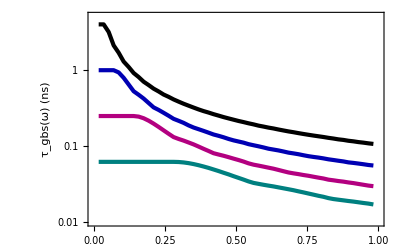

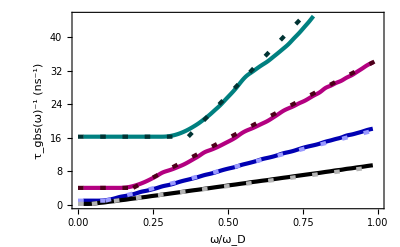

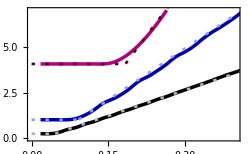

```mathematica
"STGB"
Show[ListLogPlot[{τGBExtract[τGBSList,2],
τGBExtract[τGBSList,3],τGBExtract[τGBSList,4],τGBExtract[τGBSList,5]},
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],
Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[Black,Thickness[0.0075]]},
FrameLabel->{Style["",16],Style["τ_gbs(ω) (ns)",16]},
PlotRange->{{0,1},{0.01,5}},
Joined->True,
PlotRange->All]]
Show[
ListPlot[{ΓGBExtract[τGBSList,2],
ΓGBExtract[τGBSList,3],ΓGBExtract[τGBSList,4],ΓGBExtract[τGBSList,5]},
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],
Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[Black,Thickness[0.0075]]},
FrameLabel->{Style["ω/ω_D",16],Style["τ_gbs(ω)^-1 (ns^-1)",16]},
PlotRange->{{0,1},{0,45}},
Joined->True,
InterpolationOrder->3,
PlotRange->All],
Plot[{τinvEmp[ω*ωD,1*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,2*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,4*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,8*10^-9,b,n1D]*10^-9},{ω,0,1},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}]]

Show[
ListPlot[{ΓGBExtract[τGBSList,2],ΓGBExtract[τGBSList,3],
ΓGBExtract[τGBSList,4],ΓGBExtract[τGBSList,5]},
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.01]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.01]],
Directive[RGBColor[0.,0,0.7],Thickness[0.01]],
Directive[Black,Thickness[0.01]]},
FrameLabel->{Style["",16],Style["",16]},
PlotRange->{{0,0.4},{0,7}},
ImageSize->250,
Joined->True,
InterpolationOrder->3,
PlotRange->All],
Plot[{τinvEmp[ω*ωD,1*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,2*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,4*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,8*10^-9,b,n1D]*10^-9},{ω,0,1},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}]]
```

Convert τ(ω) to t(ω) and plot

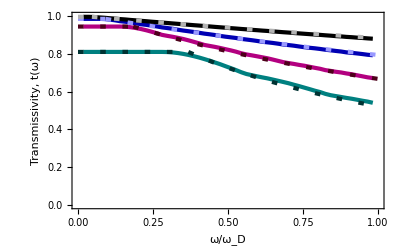

```mathematica
Show[ListPlot[{tGBExtract[τGBSList,2],tGBExtract[τGBSList,3],
tGBExtract[τGBSList,4],tGBExtract[τGBSList,5]},
PlotRange->{{0,1},{0.,1}},
FrameLabel->{"ω/ω_D","Transmissivity, t(ω)"},
Joined->True,
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],
Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[Black,Thickness[0.0075]]}],Plot[{tEmp[ω*ωD,1*10^-9,b,n1D],tEmp[ω*ωD,2*10^-9,b,n1D],tEmp[ω*ωD,4*10^-9,b,n1D],tEmp[ω*ωD,8*10^-9,b,n1D]},{ω,0,1},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}]]
```

Calculating κ_L

```mathematica
Timing[
κTList={disp};
For[i=2,i≤ 5,i++,
Print[τGBSList[[i,1]]//N];
κT={};
For[T=5,T≤ 500,T=T*1.1,
AppendTo[κT,{T,κLCalc[τTotCalc[τGBSList[[i,3]],T],T]}]];
AppendTo[κTList,{τGBSList[[i,1]]//N,τGBSList[[i,2]],κT}]]]
```

1.×10^-9

2.×10^-9

4.×10^-9

8.×10^-9

{0.280117,Null}

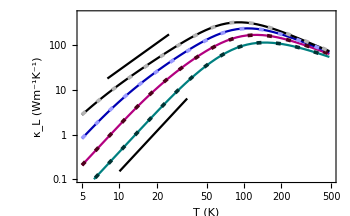

```mathematica
Show[ListLogLogPlot[{κTList[[2,3]],κTList[[3,3]],κTList[[4,3]],κTList[[5,3]]},
FrameLabel->{Style["T (K)"],Style["κ_L (Wm^-1K^-1)",SingleLetterItalics->False]},
FrameTicks->Automatic,
Joined->True,
PlotStyle->{RGBColor[0.,0.5,0.5],RGBColor[0.7,0.,0.5],RGBColor[0.,0,0.7],Black},
PlotRange->{{5,500},{0.1,500}},
ImageSize->350],
LogLogPlot[{κL[T,(τinvEmp[ω,1*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τinvEmp[ω,2*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τinvEmp[ω,4*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τinvEmp[ω,8*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}]},{T,5,500},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}],
ListLogLogPlot[{T2[18,{Tref,8,25}],T3[0.15,{Tref,10,35}]},Joined->True]]
```

```mathematica
LineLegend[{Directive[Black,Thickness[0.0075]],Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]]},
{Style["     8        2",FontFamily->"Times New Roman",18],Style["     4        5",FontFamily->"Times New Roman",18],Style["     2        10",FontFamily->"Times New Roman",18],Style["     1        19",FontFamily->"Times New Roman",18]},Spacings->0.3]
```

Supplemental: 
Pole plots of Γ^-1(k)

k=1π/d

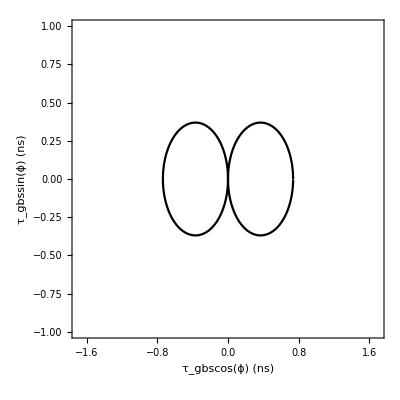

k=2π/d

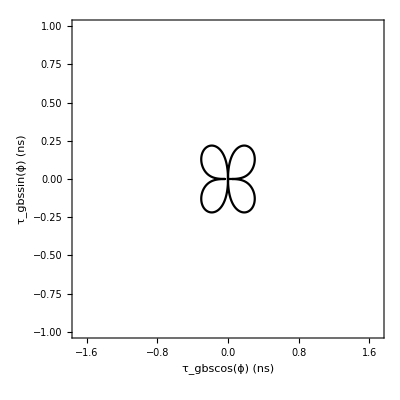

k=3π/d

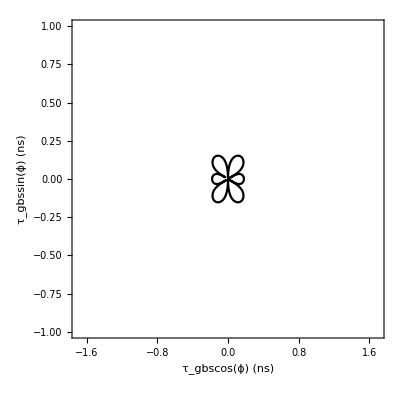

k=4π/d

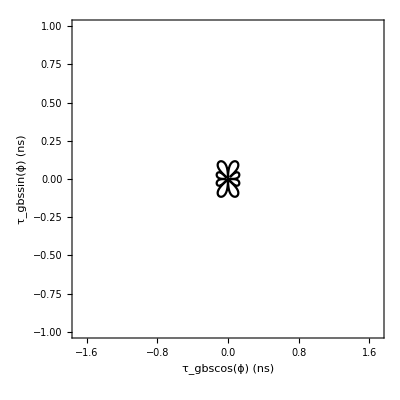

```mathematica
d=3*10^-9;
For[i=1,i≤4,i++,
Print["k="<>ToString[i]<>"π/d"];
Print[τPolarPlot[i π/d]]]
```